```mathematica
Remove["Global`*"]
```

```mathematica
SuperStar[ϕ_]:= ϕ/.Complex[u_,v_]->Complex[u,-v];
SuperPlus[v_]:= Simplify@ConjugateTranspose[v];
```

```mathematica
$Assumptions={θ∈Reals,ϕ∈Reals,t∈Reals};
<<MaTeX`;
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
```

```mathematica
HeatPlot[F_,scale_]:=Show[
SphericalPlot3D[0.5,{Theta,0,π},{Phi,0,2*π},
ColorFunction->Function[{x,y,z,Theta,Phi},ColorData["TemperatureMap"][scale*F[Theta,Phi]]],ColorFunctionScaling->False,PlotStyle->Directive[Opacity[0.9]],Boxed-> False,Axes-> False]
];
PlotBloch[{T_,F_},col_]:=Show[
Graphics3D[{Black,Opacity[0.05],Sphere[{0,0,0.5},0.5]},Boxed-> False],
Graphics3D[{Black,Thickness[0.001],Arrowheads[Medium],
Line[{{-0.5,0,0.5},{0.5,0,0.5}}],
Line[{{0,0,0},{0,0,1}}],
Line[{{0,-0.5,0.5},{0,0.5,0.5}}],
Sphere[{0.5,0,0.5},0.01],Sphere[{-0.5,0,0.5},0.01],
Sphere[{0,-0.5,0.5},0.01],Sphere[{0,0.5,0.5},0.01],
Sphere[{0,0,0},0.01],Sphere[{0,0,1},0.01],
Text[Style[MaTeX["|+\\rangle",Magnification->1.5],Large],{0.6,0,0.5}],
Text[Style[MaTeX["|-\\rangle",Magnification->1.5],Large],{-0.6,0,0.5}],
Text[Style[MaTeX["|\\uparrow\\rangle",Magnification->1.5],Large],{0,0,1.1}],
Text[Style[MaTeX["|\\downarrow\\rangle",Magnification->1.5],Large],{0,0,-0.1}],
Text[Style[MaTeX["|R\\rangle",Magnification->1.5],Large],{0,0.6,0.5}],
Text[Style[MaTeX["|L\\rangle",Magnification->1.5],Large],{0,-0.6,0.5}
]},Boxed-> False],
ParametricPlot3D[{Sin[u]/2,Cos[u]/2,0.5},{u,0,2 Pi},Boxed->False,Axes-> False,PlotStyle-> {Gray,Thickness[0.001]}],
ParametricPlot3D[{Sin[u]/2,0,Cos[u]/2+0.5},{u,0,2 Pi},Boxed->False,Axes-> False,PlotStyle-> {Gray,Thickness[0.001]}],
ParametricPlot3D[{0,Sin[u]/2,Cos[u]/2+0.5},{u,0,2 Pi},Boxed->False,Axes-> False,PlotStyle-> {Gray,Thickness[0.001]}],
ParametricPlot3D[{Sin[u]/2 Sin[T],Cos[u]/2 Sin[T],1/2 Cos[T]+1/2},{u,0,2 Pi},Boxed->False,Axes-> False,PlotStyle-> {col,Thickness[0.001]}],
Graphics3D[{col,Thickness[Large],Arrowheads[Large],Arrow[{{0,0,1/2},{1/2 Sin[T]Cos[F],1/2 Sin[T]Sin[F],1/2 Cos[T]+1/2}}]},Axes->True]
];
PlotCurveP[ϕ1_,ϕ2_,C_]:=Show[PlotBloch[{C/.ϕ->ϕ2,ϕ2},Red],ParametricPlot3D[{{0,0,1/2},{1/2 Sin[C]Cos[ϕ],1/2 Sin[C]Sin[ϕ],1/2 Cos[C]+1/2}},{ϕ,ϕ1,ϕ2},PlotStyle->Blue]]
PlotCurveT[θ1_,θ2_,C_]:=Show[PlotBloch[{θ2,C/.θ->θ2},Red],ParametricPlot3D[{{0,0,1/2},{1/2 Sin[θ]Cos[C],1/2 Sin[θ]Sin[C],1/2 Cos[θ]+1/2}},{θ,θ1,θ2},PlotStyle->Blue]]
```

## Spin 1/2 v magnetickém poli, tedy H = -μ B.S

Stavy na Blochově sféře odpovídají čistým tavům, uvnitř koule odpovídají smíšeným. Projekce z Blochovy sféry do E^3 je {1/2 Sin[θ]Cos[ϕ],1/2 Sin[θ]Sin[ϕ],1/2 Cos[θ]+1/2}.

```mathematica
Manipulate[PlotBloch[{t,p},Red],{t,0,π},{p,0,2π},ContinuousAction->True]
```

### Vlastní stavy

#### V naší konvenci

```mathematica
u1={Cos[θ/2]Exp[-I ϕ],Sin[θ/2]};
u2={-Sin[θ/2]Exp[-I ϕ],Cos[θ/2]};
```

#### v Kolodrůbežově konvenci:

```mathematica
(*u1={Cos[θ/2],Sin[θ/2]Exp[I ϕ]};
u2={Sin[θ/2],-Cos[θ/2]Exp[I ϕ]};*)
```

### Berryho konexe A_θ,A_ϕ příslušenící vlastním stavům 1,2

Berryho konexe A_a=i⟨0|∂_a |0⟩

```mathematica
A[v_,ind_]:=Simplify[I SuperStar[v].D[v,ind]];χ[v_,i_,j_]:=Simplify[SuperStar[D[v,i]].D[v,j]-(SuperStar[D[v,i]].v)(SuperStar[v].D[v,j])];
```

Dosazením vlastních stavů dostaneme

```mathematica
A1θ=A[u1,θ]
A1ϕ=A[u1,ϕ]
A2θ=A[u2,θ]
A2ϕ=A[u2,ϕ]
χ1=({{χ[u1,θ,θ], χ[u1,θ,ϕ]}, {χ[u1,ϕ,θ], χ[u1,ϕ,ϕ]}})
χ2=({{χ[u2,θ,θ], χ[u2,θ,ϕ]}, {χ[u2,ϕ,θ], χ[u2,ϕ,ϕ]}})
```

0

Cos[θ/2]^2

0

Sin[θ/2]^2

{{1/4,1/4 ⅈ Sin[θ]},{-1/4 ⅈ Sin[θ],Sin[θ]^2/4}}

{{1/4,-1/4 ⅈ Sin[θ]},{1/4 ⅈ Sin[θ],Sin[θ]^2/4}}

Metrický tenzor g=Re[χ]=(χ+χ^T)/2a Berryho křivost  F = i(χ - χ^T)

```mathematica
g1=Simplify@Re[χ1]
F1=I (χ1-Transpose@χ1) 
g2=Simplify@Re[χ2]
F2=I (χ1-Transpose@χ1)
```

{{1/4,0},{0,Sin[θ]^2/4}}

{{0,-Sin[θ]/2},{Sin[θ]/2,0}}

{{1/4,0},{0,Sin[θ]^2/4}}

{{0,-Sin[θ]/2},{Sin[θ]/2,0}}

### Gaussova křivost z Riemannova tenzoru je K=R/2=(g^μν R_μν)/2

```mathematica
Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]
```

Metin::shdw: Symbol Metin appears in multiple contexts {GRQUICK`,Global`}; definitions in context GRQUICK` may shadow or be shadowed by other definitions.

Ricci::shdw: Symbol Ricci appears in multiple contexts {GRQUICK`,Global`}; definitions in context GRQUICK` may shadow or be shadowed by other definitions.

GMET::shdw: Symbol GMET appears in multiple contexts {GRQUICK`,Global`}; definitions in context GRQUICK` may shadow or be shadowed by other definitions.

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

```mathematica
Metin[g1,{θ,ϕ}]
MatrixForm[GMET]
```

Metric Success

(1/4 | 0
0 | Sin[θ]^2/4)

```mathematica
R={{Ricci[0,0],Ricci[0,1]},{Ricci[1,0],Ricci[1,1]}}
```

{{1,0},{0,Sin[θ]^2}}

```mathematica
K=1/2 Sum[g1[[i,j]]R[[i,j]],{i,1,2},{j,1,2}]
```

1/2 (1/4+Sin[θ]^4/4)

### Integrace vzdálenosti na Blochově sféře od počátečních stavů

Změna souřadnic θ,ϕ znamená změnu orientace magnetického pole, jelikož jsme začínali s Hamiltoniánem H=-μ B.S, který jsme orientovali do směru osy z, tedy B=(0,0 B_z), což ve sférických souřadnicích dalo právě ty vlastní vektory, které používáme. Vzdálenost na varietě je s=(∫_a1)^a2(∫_b1)^b2 χ_ij dλ^i dλ^j. Uvažme λ=(θ
ϕ), což odpovídá stáčení směru osy z, tedy změně orientace magnetického pole. Integrujme geometrický tenzor podél křivky C tvaru ϕ=ϕ(θ) (funkce s2T), nebo θ=θ(ϕ) (funkce s2P). Je tedy nutné využít tu, kde derivace ϕ’  resp. θ’ není nulová.

```mathematica
χ=χ1;
s2T[T1_,T2_,C_]:=Integrate[(Sqrt[χ[[1,1]]+χ[[2,2]]D[C,θ]])/.ϕ->C,{θ,T1,T2}]
s2P[P1_,P2_,C_]:=Integrate[(Sqrt[χ[[1,1]]D[C,ϕ]]+χ[[2,2]])/.θ->C,{ϕ,P1,P2}]
```

```mathematica
path[ϕ_]:=Sqrt@ϕ
N@s2P[0,2π,path[ϕ]]
Manipulate[PlotCurveP[0,ff,path[ϕ]],{ff,10^-5,2π}]
```

2.99944

#### Vzdálenost s^2 od stavu |↑⟩

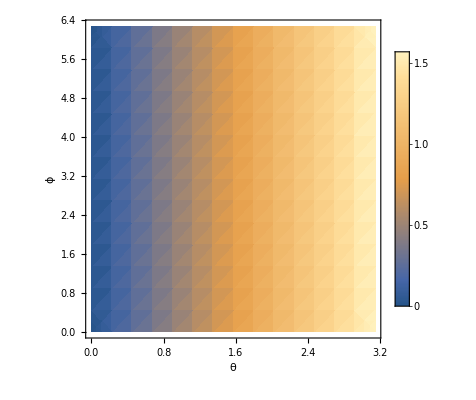

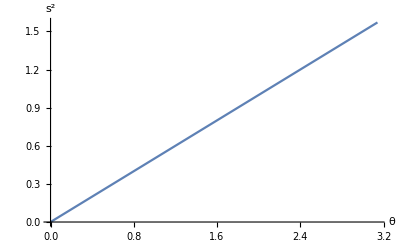

```mathematica
DensityPlot[Evaluate@s2T[0,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotLegends->Automatic,FrameLabel->Automatic]
Plot[Evaluate@s2T[0,θ,0],{θ,0,π},PlotLegends->Automatic,AxesLabel->{"θ","s^2"}]
```

### Berryho úhel

Z Berryho konexe lze dostat Berryho křivost F_ab=∂_a A_b-∂_b A_a. Tu jsme taky dostali dříve antisymetrizací χ_ab.  Berryho úhel je pak ϕ_B =∮_C A_a dλ^a= ∫_S F_ab dλ^a⋀dλ^b. Skutečně vezmeme-li F1 vypočítané antisymetrizací χ a F definované na začátku tohoto odstavce, dostaneme stejné matice:

```mathematica
F=F1
Aθ=A1θ;
Aϕ=A1ϕ;
FzA=Simplify@{{D[Aθ,θ]-D[Aθ,θ],D[Aϕ,θ]-D[Aθ,ϕ]},{D[Aθ,ϕ]-D[Aϕ,θ],D[Aϕ,ϕ]-D[Aϕ,ϕ]}}
```

{{0,-Sin[θ]/2},{Sin[θ]/2,0}}

{{0,-Sin[θ]/2},{Sin[θ]/2,0}}

Pro ϕ = ϕ (θ), resp. θ = θ (ϕ):

```mathematica
A={A1θ,A1ϕ}
ϕBT[θ1_,θ2_,C_]:=Integrate[(A[[1]]+A[[2]]D[C,θ])/.ϕ->C,{θ,θ1,θ2}];  
ϕBP[ϕ1_,ϕ2_,C_]:=Integrate[(A[[1]]D[C,ϕ]+A[[2]])/.θ->C,{ϕ,ϕ1,ϕ2}];
(*Změna na NIntegrate urychlí výpočet, ale expression je lepší*)
```

{0,Cos[θ/2]^2}

#### Příklad integrační křivky, která mění znaménko vlnové funkce

Integrace po C=cos(θ) od 0 do kπ dává ϕ_B=0 pro k sudé a ϕ_B=1 pro k liché:

```mathematica
ϕBT[0,π,Cos[θ]]
Manipulate[Show[
Evaluate@PlotCurveT[0,ff,Cos[θ]],ParametricPlot3D[{r/2 Cos@a+h(√3)/2,r Sin@a,-r(√3)/2 Cos@a+h/2+1/2}/.{r-> 0.431,h-> 0.259},{a,0,2π}]],{{ff,2π},0.1,2π}]
```

-1

Mějme ϕ=konst, ϕ_B=∮_C A_a dλ^a= (∫_0)^(2π)(A_1+A_2 dϕ/dθ)dθ=(∫_0)^(2π)A_1 dθ=0:

```mathematica
ϕBT[0,π,2]
```

0

Vezmeme-li křivku, viz válcová výseč v grafu (je to případ z prvního Berryho článku, str. 52 nehoře), tak bychom dle článku měli naintegrovat ϕ_B=-1 pro úhel π po dané křivce:

```mathematica
{#,N@#}&@ϕBP[0,π,2Cos[ϕ]]
Manipulate[Show[
Evaluate@PlotCurveP[0,ff,2Cos[ϕ]],ParametricPlot3D[{r/2 Cos@a+h(√3)/2,r Sin@a,-r(√3)/2 Cos@a+h/2+1/2}/.{r-> 0.431,h-> 0.259},{a,0,2π}]],{{ff,π},0.1,π}]
```

{1/2 π (1+BesselJ[0,2]),1.92248}

Což nevychází stejně, mam dobře tu křivku vůbec?

#### Berryho fáze od stavu |↑⟩

Integrování fáze po obvodu až do ϕ pro konstantní θ. Berryho fáze je  ϕ_B=∮_C A_a dλ^a= (∫_0)^ϕ(A_1 dθ/dϕ+A_2)dϕ=(∫_0)^ϕ A_2 dϕ=cos^2(θ/2)ϕ, což je to samé, jako dosazení  za křivky dosadit C=θ (pak totiž D[C,θ]=dθ/dϕ=0) do ϕBP.

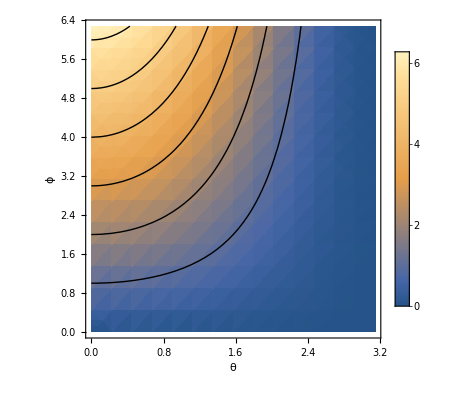

```mathematica
Show[DensityPlot[Evaluate@ϕBP[0,ϕ,θ],{θ,0,π},{ϕ,0,2π},PlotLegends->Automatic,FrameLabel->Automatic],ContourPlot[Evaluate@ϕBP[0,ϕ,θ],{θ,0,π},{ϕ,0,2π},ContourShading->None]]
```

Což bude problém singularity souřadnic pro θ = 0, ta Berryho fáze zde asi nelze takto počítat, ale vychází to k tomu spojitě, takže něco na tom bude.

Pozorovatelný význam má jen pro ϕ = 2 π (kvůli interferenci s původním svazkem se musí stav vrátit na původní souřadnici parametrického prostoru). Tato Beryho fáze pak je:

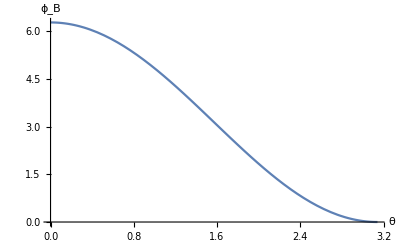

```mathematica
Plot[Evaluate@ϕBP[0,2π,θ],{θ,0,π},AxesLabel->{θ,Subscript[ϕ, B]}]
```

# Couterdiabatic driving - změna směru magnetického pole

Příklad z berryho třetího článku, str. 2 - 5. Hamiltonián H_0=γ B(t).S, pro S=1/2((0 | 1
1 | 0),(0 | -i
i | 0),(1 | 0
0 | -1)) a zvolme B(t)=(Sin[t]
0
-Cos[t]),γ=1 .
Obecně bude spin v takovém poli precesovat kolem osy b(t):=(B(t))/(|B(t)|) rychlostí γB(t). Existují však Hamiltoniány vytvořené jako H_0+H_CD, které této precesi zabrání. Pro magnetické pole B0(t) lze toto pole vytvořit, jako B(t) = B_0(t) + 1/γ b_0(t)×∂_t b_0(t).

```mathematica
S={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
B0[t_]={Sin[t],0,-Cos[t]}
b0[t_]=Simplify@(B0[t]/Norm[B0[t]])
B[t_]=Simplify[B0[t]+1/γ b0[t]×D[b0[t],t]]
h0[t_]=B0[t].S
h[t_]=B[t].S
```

{Sin[t],0,-Cos[t]}

{Sin[t],0,-Cos[t]}

{Sin[t],-1/γ,-Cos[t]}

{{-Cos[t],Sin[t]},{Sin[t],Cos[t]}}

{{-Cos[t],ⅈ/γ+Sin[t]},{-ⅈ/γ+Sin[t],Cos[t]}}

### Transformace up stavu v čase

```mathematica
Exp[I h0[t] t].u1
```

{ⅇ^(-ⅈ ϕ-ⅈ t Cos[t]) Cos[θ/2]+ⅇ^(ⅈ t Sin[t]) Sin[θ/2],ⅇ^(-ⅈ ϕ+ⅈ t Sin[t]) Cos[θ/2]+ⅇ^(ⅈ t Cos[t]) Sin[θ/2]}

```mathematica
h0[t].u1
h[t].u1
rb0=Simplify@Solve[a u1+b u2== h0[1].u1,{a,b}]
rb1=Simplify@Solve[a u1+b u2== h[1].u1,{a,b}]
```

{-ⅇ^(-ⅈ ϕ) Cos[t] Cos[θ/2]+Sin[t] Sin[θ/2],ⅇ^(-ⅈ ϕ) Cos[θ/2] Sin[t]+Cos[t] Sin[θ/2]}

{-ⅇ^(-ⅈ ϕ) Cos[t] Cos[θ/2]+(ⅈ+Sin[t]) Sin[θ/2],ⅇ^(-ⅈ ϕ) Cos[θ/2] (-ⅈ+Sin[t])+Cos[t] Sin[θ/2]}

{{a→-Cos[1] Cos[θ/2]^2+Cos[1] Sin[θ/2]^2+1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) Sin[1] Sin[θ],b→ⅇ^(-ⅈ ϕ) Cos[θ/2]^2 Sin[1]-ⅇ^(ⅈ ϕ) Sin[1] Sin[θ/2]^2+Cos[1] Sin[θ]}}

{{a→-Cos[1] Cos[θ]+1/2 ⅇ^(-ⅈ ϕ) (-ⅈ+Sin[1]+ⅇ^(2 ⅈ ϕ) (ⅈ+Sin[1])) Sin[θ],b→ⅇ^(-ⅈ ϕ) Cos[θ/2]^2 (-ⅈ+Sin[1])-ⅇ^(ⅈ ϕ) (ⅈ+Sin[1]) Sin[θ/2]^2+Cos[1] Sin[θ]}}

```mathematica
Manipulate[
T=t;
Fg01[θ_,ϕ_]=ComplexExpand[Re[(h0[T].u1)[[1]]]];
Fg02[θ_,ϕ_]=ComplexExpand[Re[(h0[T].u1)[[2]]]];
Fg1[θ_,ϕ_]=ComplexExpand[Re[(h[T].u1)[[1]]]];
Fg2[θ_,ϕ_]=ComplexExpand[Re[(h[T].u1)[[2]]]];
GraphicsGrid[{{HeatPlot[Fg01,1],HeatPlot[Fg1,1]},{HeatPlot[Fg02,1],HeatPlot[Fg2,1]}}],{t,0,π}]
```

#### Nastavení vývoje magnetického pole podle žádaného vývoje spinu

Úlohu lze formulovat i naopak, tedy chceme měnit orientaci spinu (tedy ho záhnout po určité trajektorii v prostoru (θ, ϕ)). Toho lze docílit dosazením do vztahu (berry 3, str. 5) B(t)=|B_0(t)|S(t)+1/γ S(t)×∂_t S(t) , kde S(t)=⟨ψ_n(t)|S|ψ_n(t)⟩ (celým Hamiltoniánem vyvinuté vektory).

```mathematica
u=u1;
ψn[T_]=Exp[-I E T-Integrate[u[[1]]D[u[[1]],t]+u[[2]]D[u[[2]],t],{t,0,T}]]u
Manipulate[DensityPlot[ComplexExpand[Re[(ψn[t])[[1]]]],{θ,0,π},{ϕ,0,π}],{t,0,5}]
```

{ⅇ^(-ⅈ ϕ) Cos[θ/2],Sin[θ/2]}

```mathematica
u1
```

{ⅇ^(-ⅈ ϕ) Cos[θ/2],Sin[θ/2]}

```mathematica
u2
```

{-ⅇ^(-ⅈ ϕ) Sin[θ/2],Cos[θ/2]}

```mathematica
ψn[0]
```

{ⅇ^(-ⅈ ϕ) Cos[θ/2],Sin[θ/2]}